```mathematica
Multiway Minkowski Music Space
```

```mathematica
s1 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-01.wav"]
s2 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-02.wav"]
s3 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-03.wav"]
s4 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-04.wav"]
s5 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-5.wav"]
s6 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-06.wav"]
s7 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-07.wav"]
s8 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-08.wav"]
s9 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-09.wav"]
s10 = Import[ "C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-10.wav"]
```

```mathematica
AudioPlot[s]
```

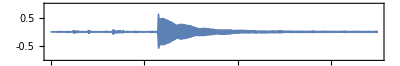
```mathematica
-Graphics-
ListLinePlot[AudioData[s][[1]]]
```

-Graphics-

-Graphics-

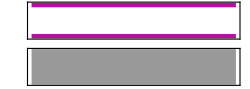
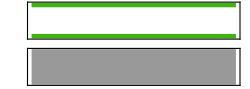
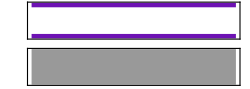
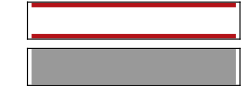

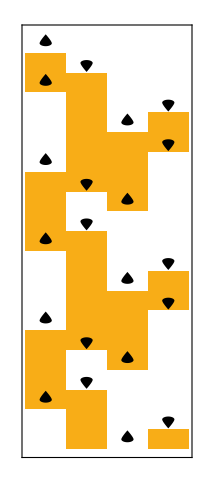

```mathematica
-Graphics-

instruments={"Harpsichord","Marimba","Sitar","Flute"};

sounds=Sound[SoundNote[{"C","G"},1,#]]&/@instruments

RulePlot[TuringMachine[2506],{1,{0,0,0,0}},20]
```